## Matrix Element calculation (including time evolution)

```mathematica
Clear[ω,ωt,t]
```

```mathematica
L =0.4*10^-6; Lstep =0.1*10^-7; LN = 2*L/Lstep + 1;nmax = 15.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
Uprop[t_,ωt_]:= Table[ Exp[(ⅈ m ωt (-2 x xt+(x^2+xt^2) Cos[t ωt]) Csc[t ωt])/(2 hbar)]*(Sqrt[-((I m)/(hbar t))]/Sqrt[2 π]+(Sqrt[-((I m)/(hbar t))] ωt^2 t^2)/(12 Sqrt[2 π])+(Sqrt[-((I m)/(hbar t))] ωt^4 t^4)/(160 Sqrt[2 π])+(61 Sqrt[-((I m)/(hbar t))] ωt^6 t^6)/(120960 Sqrt[2 π])),{x,-L,L,Lstep},{xt,-L,L,Lstep}];

ψ[ n_, ω_]:= Normalize[Table[1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Srt[(m ω)/hbar]x],{x,-L,L,Lstep}]];
ψf[ nt_, ωt_]:=  Normalize[Table[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt],{xt,-L,L,Lstep}]];
```

```mathematica
psi[t_,ω_,ωt_, n_] := Normalize[ψ[n, ω]. Uprop[t,ωt]]
Monitor[evolmat = Table[psi[t, omega[5],omega[5], 3],{t,0,6000 10^-9, 70 10^-9}];,{(t/(2000 10^-9))//N}]
MatrixPlot[evolmat,PlotLegends -> True]
```

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

$Aborted

MatrixPlot::mat0: Argument evolmat at position 1 is not a matrix.

MatrixPlot[evolmat,PlotLegends→True]

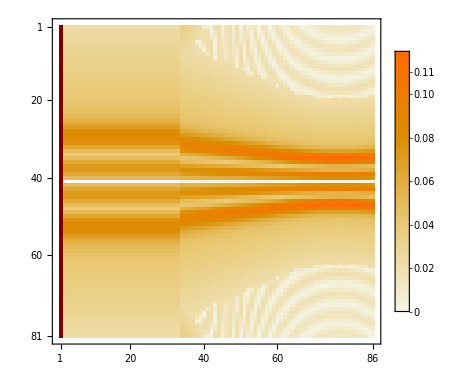

```mathematica
MatrixPlot[Table[Abs[evolmat[[i,j]]]^2,{j,1,Length[evolmat[[1]]]},{i,1,Length[evolmat[[All,1]]]}],PlotLegends -> True]
```

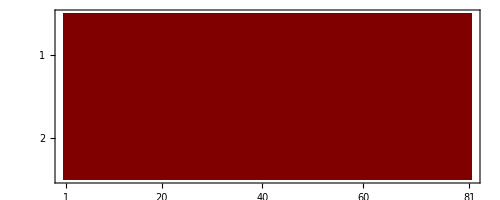

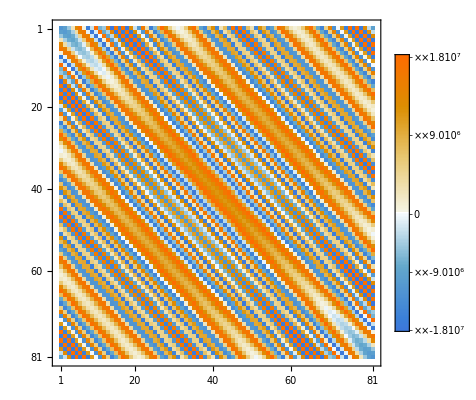

```mathematica
MatrixPlot[{ψ[4,10^5],ψ[4,10^5]}]
MatrixPlot[Uprop[10^-6,10^5], PlotLegends -> True]
```

## Calculate matrix elements for all segments (Are the decay times of the order of typical ωt? Here: assumed much smaller)

```mathematica
(*from LambDickeParams_Singe.py @532nm and @10**7 lattice beam intensity *)
(*levels=["6s 2 S 1/2","7p 2 P ?3/2","7s 2 S 1/2","6p 2 P ?1/2","6p 2 P ?3/2","5d 2 D 3/2","5d 2 D 5/2"]*)
(*decays=[l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34]*)
omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};
etas = {0.697646827167697,0.14448683087878345,0.17095247621856766,0.35533728030290285,0.10383570605450117,0.3729352538139725,0.06952852571696208,0.07198024772090308,0.19467123685222815,0.21390857630773225,0.23003214721947357};
l21=455.5*10^-9;
l23=2931.8*10^-9;
l35=1469.9*10^-9;
l41=894.3*10^-9;
l64=3011.1*10^-9;
l51=852.1*10^-9;
l65=3614.1*10^-9;
l75=3491*10^-9;
l27=1360.6*10^-9;
l26=1342.8*10^-9;
l34=1359.2*10^-9;
decays={l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34};
g23=4.05*10^6;
g34=6.23*10^6;
g35=11.4*10^6;
g41=28.6*10^6;
g26=0.13*10^6;
g27=1.10*10^6;
g75=0.78*10^6;
g65=0.11*10^6;
g51=32.8*10^6;
g64=0.91*10^6;
g21=1.84*10^6;
gammas={g21,g23,g35,g41,g64,g51,g65,g75,g27,g26,g34};
omega[n_]:= omegas[[n]]/1.01
eta[n_]:= etas[[n]]
nmax = 30;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
L =0.6*10^-6; Lstep =0.09*10^-7; LN = 2*L/Lstep + 1;deltak = 2 Pi/(455 10^-9)//N;
ωg = omega[1];
```

```mathematica
Clear[t]
```

```mathematica
(*IntU[ω_,ωt_,τ_]:= Monitor[tstart = τ/10;tstop = 3*τ //N; tstep =(tstop/5)//N;*)
IntU[ω_,ωt_,τ_]:= Monitor[tstart =2.5 10^6;tstop = 2.5 10^-6 //N; tstep =τ//N; t =τ;uma = Table[
Lstep^2 *NIntegrate[1/Sqrt[2^nt nt!]((m ωg)/(Pi hbar))^(1/4)Exp[(-m ωg xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωg)/hbar]xt]*1/Sqrt[2^n n!]((m ωg)/(Pi hbar))^(1/4)Exp[(-m ωg x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ωg)/hbar]x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}],{n,0.,nmax},{nt,0.,nmax}] ,{n,nt,t//N}];(*Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}] Exp[-t/τ]/τ,{t,tstart, tstop, tstep}],{n,nt,t//N}]*)
Drw[n_,nt_, η_, θ_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[θ])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[θ])^2]Exp[-(η  Cos[θ])^2/2];
IntDr[η_]:= Table[√((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[Pi/4])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[Pi/4])^2]Exp[-(η  Cos[Pi/4])^2/2],{n,0.,nmax},{nt,0.,nmax}];
IntD[η_]:= ParallelTable[√((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  1)^2]Exp[-(η  1)^2/2],{n,0.,nmax},{nt,0.,nmax}];
```

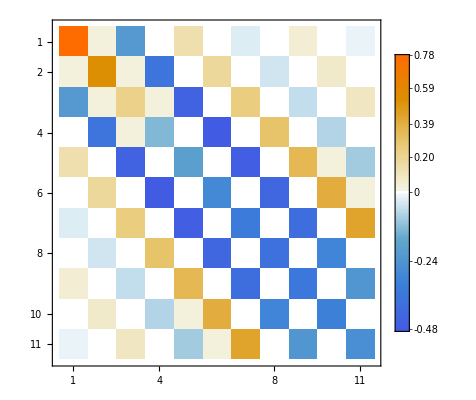

```mathematica
MatrixPlot[IntD[0.7], PlotLegends -> True] (*test*)
```

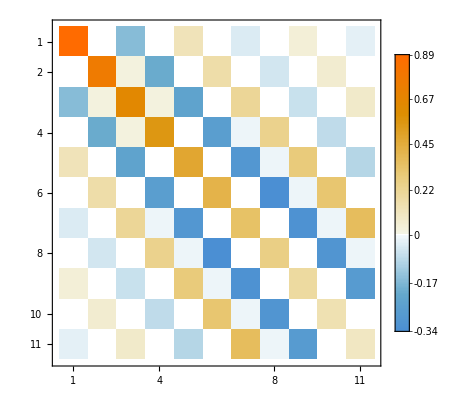

```mathematica
MatrixPlot[IntDr[0.7], PlotLegends -> True] (*test*)
```

```mathematica
U12= IntU[omega[1],omega[2], (1/g21) //N];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

$Aborted

```mathematica
MatrixPlot[U12]
```

```mathematica
U23 = IntU[omega[2],omega[3], (1/g23) //N];
```

```mathematica
U34 = IntU[omega[3],omega[4], (1/g34) //N];
```

```mathematica
omega[5]
omega[1]
```

147900.

92479.6

```mathematica
U51 = IntU[omega[5]/2,omega[1], (1/g51) //N]
```

{{0.0597517+0.998124 ⅈ,0.000727866+0.000589838 ⅈ,0.000942779-0.00131688 ⅈ,0.00580463+0.00365238 ⅈ,0.00403335-0.00734932 ⅈ,0.0248525+0.0117677 ⅈ,0.0102442-0.0254615 ⅈ,0.0721514+0.0241365 ⅈ,0.0171046-0.0634989 ⅈ,0.157461+0.0324801 ⅈ,0.0178027-0.123016 ⅈ},{0.000727866+0.000589838 ⅈ,-0.176888-0.985762 ⅈ,0.00893252+0.00562051 ⅈ,0.00671709-0.0122395 ⅈ,0.0431751+0.0204435 ⅈ,0.0180961-0.0449767 ⅈ,0.127019+0.042491 ⅈ,0.0294927-0.109489 ⅈ,0.261628+0.0539672 ⅈ,0.0280404-0.193758 ⅈ,0.401809+0.0338396 ⅈ},{0.000942779-0.00131688 ⅈ,0.00893252+0.00562051 ⅈ,0.301829+0.941679 ⅈ,0.0537595+0.0254553 ⅈ,0.0234551-0.0582963 ⅈ,0.166812+0.055803 ⅈ,0.0383828-0.142492 ⅈ,0.330536+0.0681814 ⅈ,0.0336617-0.232601 ⅈ,0.447075+0.0376518 ⅈ,0.0063055-0.259232 ⅈ},{0.00580463+0.00365238 ⅈ,0.00671709-0.0122395 ⅈ,0.0537595+0.0254553 ⅈ,-0.380512-0.976912 ⅈ,0.187208+0.0626258 ⅈ,0.0434773-0.161405 ⅈ,0.368379+0.0759873 ⅈ,0.0359438-0.24837 ⅈ,0.442519+0.0372681 ⅈ,0.00550062-0.226142 ⅈ,0.27874-0.00986655 ⅈ},{0.00403335-0.00734932 ⅈ,0.0431751+0.0204435 ⅈ,0.0234551-0.0582963 ⅈ,0.187208+0.0626258 ⅈ,0.556934+0.691628 ⅈ,0.384207+0.0792522 ⅈ,0.0365314-0.252431 ⅈ,0.421241+0.0354761 ⅈ,0.00457011-0.187886 ⅈ,0.163321-0.0057811 ⅈ,0.00158772+0.0166469 ⅈ},{0.0248525+0.0117677 ⅈ,0.0180961-0.0449767 ⅈ,0.166812+0.055803 ⅈ,0.0434773-0.161405 ⅈ,0.384207+0.0792522 ⅈ,-0.573923-1.04486 ⅈ,0.405435+0.034145 ⅈ,0.00390043-0.160354 ⅈ,0.0816873-0.00289155 ⅈ,0.0069756+0.0731407 ⅈ,-0.282546+0.0440856 ⅈ},{0.0102442-0.0254615 ⅈ,0.127019+0.042491 ⅈ,0.0383828-0.142492 ⅈ,0.368379+0.0759873 ⅈ,0.0365314-0.252431 ⅈ,0.405435+0.034145 ⅈ,0.704172+0.563081 ⅈ,0.040788-0.00144386 ⅈ,0.00983917+0.103166 ⅈ,-0.316276+0.0493485 ⅈ,0.0405618+0.186199 ⅈ},{0.0721514+0.0241365 ⅈ,0.0294927-0.109489 ⅈ,0.330536+0.0681814 ⅈ,0.0359438-0.24837 ⅈ,0.421241+0.0354761 ⅈ,0.00390043-0.160354 ⅈ,0.040788-0.00144386 ⅈ,-0.769812-0.512735 ⅈ,-0.326963+0.0510159 ⅈ,0.0379473+0.174197 ⅈ,-0.14023+0.0394379 ⅈ},{0.0171046-0.0634989 ⅈ,0.261628+0.0539672 ⅈ,0.0336617-0.232601 ⅈ,0.442519+0.0372681 ⅈ,0.00457011-0.187886 ⅈ,0.0816873-0.00289155 ⅈ,0.00983917+0.103166 ⅈ,-0.326963+0.0510159 ⅈ,0.88629+0.696868 ⅈ,-0.107145+0.0301315 ⅈ,-0.0240482-0.0693484 ⅈ},{0.157461+0.0324801 ⅈ,0.0280404-0.193758 ⅈ,0.447075+0.0376518 ⅈ,0.00550062-0.226142 ⅈ,0.163321-0.0057811 ⅈ,0.0069756+0.0731407 ⅈ,-0.316276+0.0493485 ⅈ,0.0379473+0.174197 ⅈ,-0.107145+0.0301315 ⅈ,-0.933253-0.50063 ⅈ,0.274116-0.113857 ⅈ},{0.0178027-0.123016 ⅈ,0.401809+0.0338396 ⅈ,0.0063055-0.259232 ⅈ,0.27874-0.00986655 ⅈ,0.00158772+0.0166469 ⅈ,-0.282546+0.0440856 ⅈ,0.0405618+0.186199 ⅈ,-0.14023+0.0394379 ⅈ,-0.0240482-0.0693484 ⅈ,0.274116-0.113857 ⅈ,0.885816+0.179639 ⅈ}}

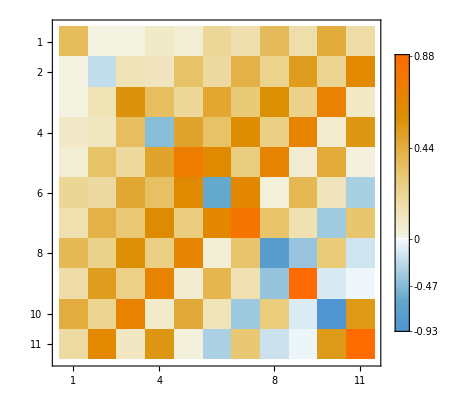

```mathematica
MatrixPlot[U51, PlotLegends -> True]
```

Power::indet: Indeterminate expression (0.+0. ⅈ)^0 encountered.

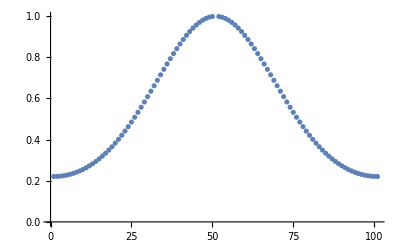

```mathematica
ListPlot[Table[Abs[Drw[15,15, 0.2, θ]]^2,{θ,0, Pi, Pi/100}]]
```

```mathematica
0
```

```mathematica
U12= IntU[omega[1],omega[2], (1/g21) //N];
U23 = IntU[omega[2],omega[3], (1/g23) //N];
U35 = IntU[omega[3],omega[5], (1/g35) //N];
U41 = IntU[omega[4],omega[1], (1/g41) //N];
U64 = IntU[omega[6],omega[4], (1/g64) //N];
U51 = IntU[omega[5],omega[1], (1/g51) //N];
U65 = IntU[omega[6],omega[5], (1/g65) //N];
U75 = IntU[omega[7],omega[5], (1/g75) //N];
U27 = IntU[omega[2],omega[7], (1/g27) //N];
U26 = IntU[omega[2],omega[6], (1/g26) //N];
U34 = IntU[omega[3],omega[4], (1/g34) //N];
```

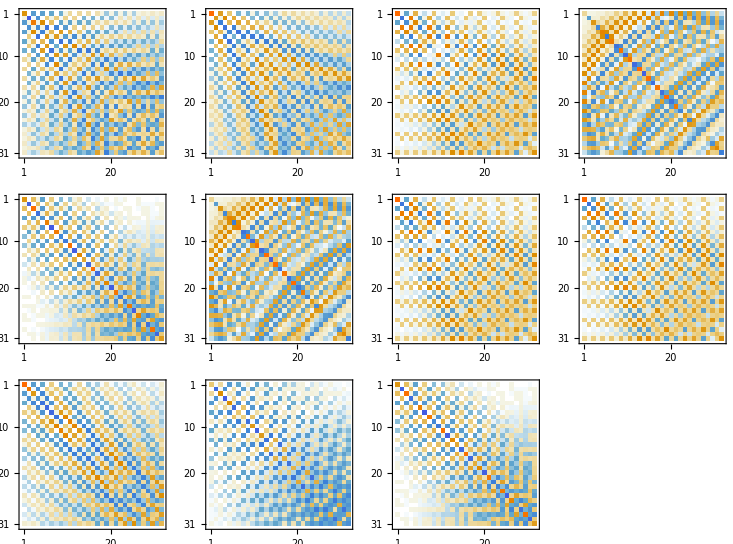

```mathematica
GraphicsGrid[{{MatrixPlot[U12],MatrixPlot[U23],MatrixPlot[U35],MatrixPlot[U41]},{MatrixPlot[U64],MatrixPlot[U51],MatrixPlot[U65],MatrixPlot[U75]},{MatrixPlot[U27],MatrixPlot[U26],MatrixPlot[U34]}}]
```

```mathematica
(*omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};*)
```

```mathematica
D12 = IntD[eta[1]];
D21 = IntDr[eta[1]];
D23 = IntDr [eta[2]];
D35 = IntDr[eta[3]];
D41 = IntDr[eta[4]];
D64 = IntDr[eta[5]];
D51 = IntDr[eta[6]];
D65 = IntDr[eta[7]];
D75 = IntDr[eta[8]];
D27 = IntDr[eta[9]];
{{D26 = IntDr[eta[10]];}, {D34 = IntDr[eta[11]];}}
```

{{Null},{Null}}

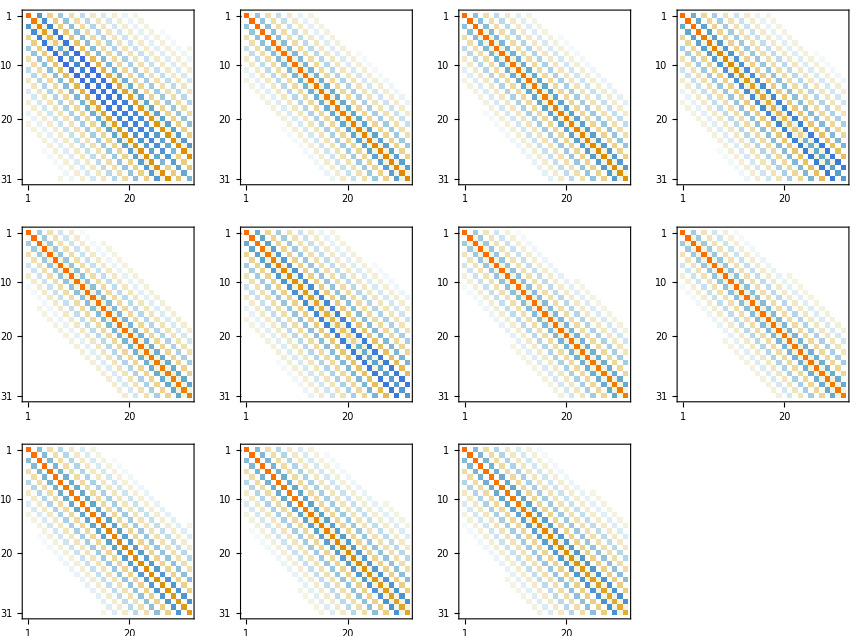

```mathematica
GraphicsGrid[{{MatrixPlot[D21],MatrixPlot[D23],MatrixPlot[D35],MatrixPlot[D41]},{MatrixPlot[D64],MatrixPlot[D51],MatrixPlot[D65],MatrixPlot[D75]},{MatrixPlot[D27],MatrixPlot[D26],MatrixPlot[D34]}}]
```

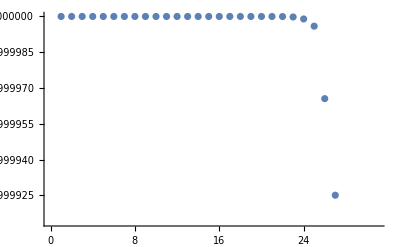

```mathematica
ListPlot[Table[Total[Table[Abs[U34[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}]]
```

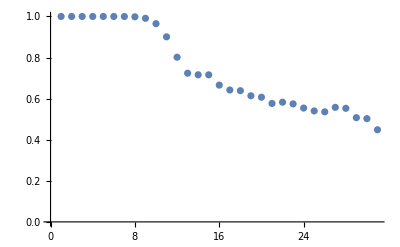

```mathematica
ListPlot[Table[Total[Table[Abs[(D21.D21.D21.D21.D21)[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}]]
```

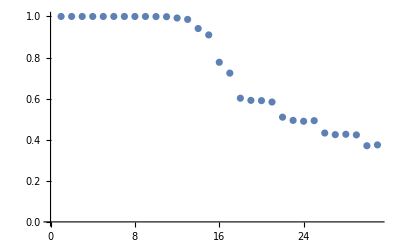

```mathematica
ListPlot[Table[Total[Table[Abs[U23[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}]]
```

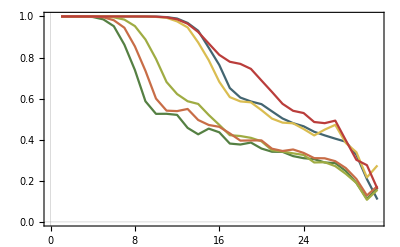

```mathematica
Show[{ListPlot[Table[Total[Table[Abs[pathA[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][1/6], Joined -> True, PlotTheme -> "Scientific"],ListPlot[Table[Total[Table[Abs[pathB[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][2/6],Joined -> True,PlotTheme -> "Scientific"],ListPlot[Table[Total[Table[Abs[pathC[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][3/6],Joined -> True,PlotTheme -> "Scientific"],ListPlot[Table[Total[Table[Abs[pathD[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][4/6],Joined -> True,PlotTheme -> "Scientific"],ListPlot[Table[Total[Table[Abs[pathE[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][5/6],Joined -> True,PlotTheme -> "Scientific"],ListPlot[Table[Total[Table[Abs[pathF[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][6/6],Joined -> True,PlotTheme -> "Scientific"]}]
```

```mathematica
pathA = D41.U34.D34.U23.D23.U12.D12; (*7p3/2 -> 7s1/2 -> 6p1/2-> 6s1/2*)
pathB = D51.U35.D35.U23.D23.U12.D12;(*7p3/2 -> 7s1/2 -> 6p3/2-> 6s1/2*)
pathC = D51.U65.D65.U26.D26.U12.D12;(*7p3/2 -> 5d3/2 -> 6p3/2-> 6s1/2*)
pathD = D41.U64.D64.U26.D26.U12.D12;(*7p3/2 -> 5d3/2 -> 6p1/2-> 6s1/2*)
pathE = D51.U75.D75.U27.D27.U12.D12;(*7p3/2 -> 5d5/2 -> 6p1/2-> 6s1/2*)
pathF = D21.U12.D12;(*7p3/2 -> 6s1/2*)

paths ={pathA, pathB, pathC, pathD, pathE, pathF};

PathA = Table[Abs[pathA[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathB = Table[Abs[pathB[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathC = Table[Abs[pathC[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathD = Table[Abs[pathD[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathE = Table[Abs[pathE[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathF = Table[Abs[pathF[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathTot = 0.201004*PathA +0.3678 PathB +0.001969 PathC + 0.016289PathD + 0.154494PathE + 0.258427 PathF;
Paths ={PathA, PathB, PathC, PathD, PathE, PathF, PathTot};
```

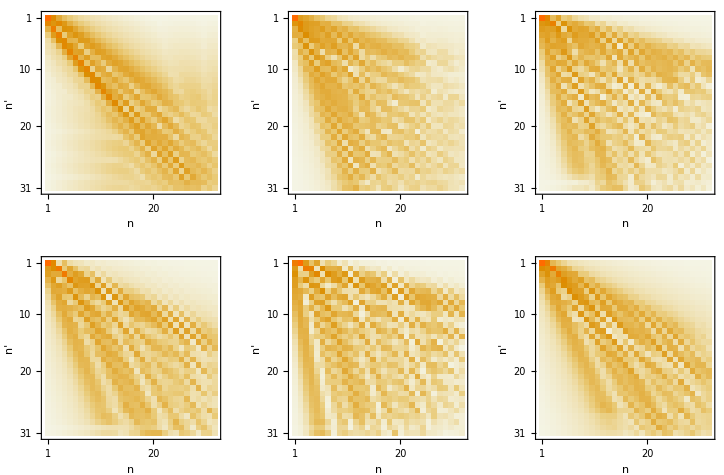

```mathematica
GraphicsGrid[{{MatrixPlot[PathA,FrameLabel -> {{"n","Path A: 2 -> 3 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black ],
MatrixPlot[PathB,FrameLabel -> {{"n","Path B: 2 -> 3 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ],
MatrixPlot[PathC,FrameLabel -> {{"n","Path C: 2 -> 6 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ]
},
{MatrixPlot[PathD,FrameLabel -> {{"n","Path D: 2 -> 6 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black ],
MatrixPlot[PathE,FrameLabel -> {{"n","Path E: 2 -> 7 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ],
MatrixPlot[PathF,FrameLabel -> {{"n","Path F: 2 -> 1"},{"n'",""}},FrameStyle-> Black ]}}, FrameStyle-> Black]
```

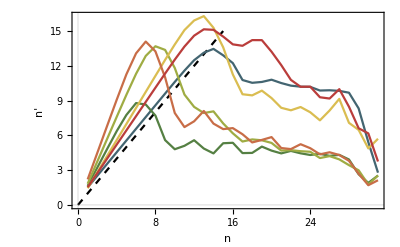

```mathematica
plotPath[pa_]:=ListPlot[Table[Sum[Paths[[pa]][[r,All]][[ra]] ra,{ra,1,nmax+1}],{r,1,Length[Paths[[pa]][[1,All]]]}],PlotStyle -> ColorData["DarkRainbow"][pa/6],Joined -> True]
Show[{Plot[x,{x,0,15}, PlotStyle -> Directive[Black, Dashed], PlotTheme -> "Scientific"],Table[plotPath[p],{p,1,6}]},PlotRange-> All, FrameLabel->{"n", "n'"}, FrameStyle -> Black]
```

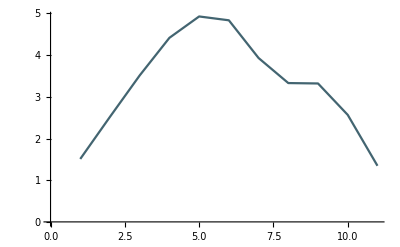
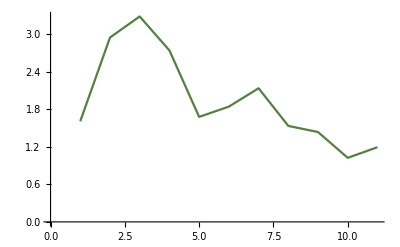
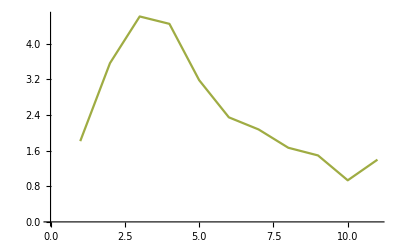
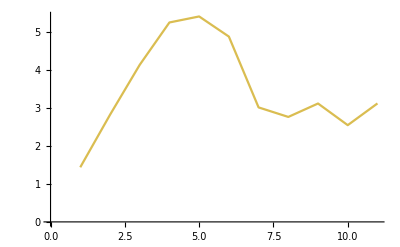
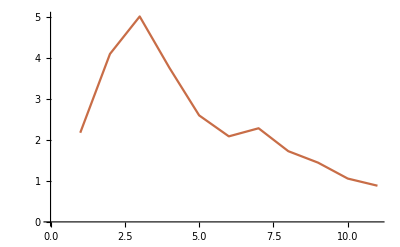
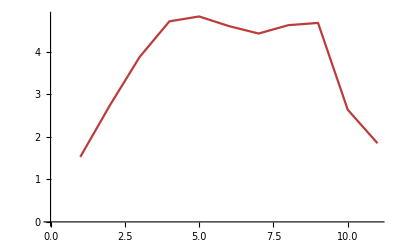

```mathematica
Table[plotPath[p],{p,1,6}]
```

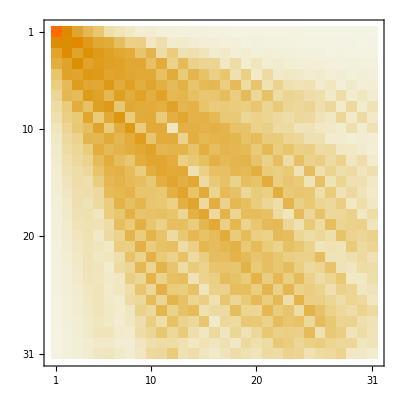

```mathematica
MatrixPlot[PathTot]
```

```mathematica
paths ={PathA, PathB, PathC, PathD, PathE, PathF, PathTot};
```

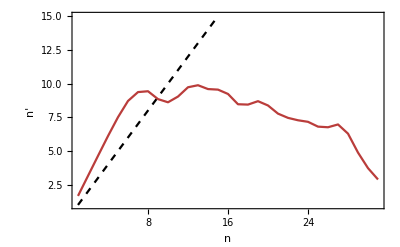

```mathematica
plotPath[pa_]:=ListPlot[Table[Sum[Paths[[pa]][[r,All]][[ra]] ra,{ra,1,nmax+1}],{r,1,Length[Paths[[pa]][[1,All]]]}],PlotStyle -> ColorData["DarkRainbow"][pa/6],Joined -> True]
Show[{Plot[x,{x,1,15}, PlotStyle -> Directive[Black, Dashed], PlotTheme -> "Scientific"],Table[plotPath[p],{p,7,7}]},PlotRange-> All, FrameLabel->{"n", "n'"}, FrameStyle -> Black]
```

```mathematica
Clear[m,hbar]
```

```mathematica
Series [((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{t,0,6}]
```

ⅇ^((0.+1.04633×10^9 ⅈ) ωt (-2 x xt+(x^2+xt^2) Cos[t ωt]) Csc[t ωt]) (1. √(-(0.+3.33057×10^8 ⅈ)/t)+0.0833333 √(-(0.+3.33057×10^8 ⅈ)/t) ωt^2 t^2+0.00625 √(-(0.+3.33057×10^8 ⅈ)/t) ωt^4 t^4+0.000504299 √(-(0.+3.33057×10^8 ⅈ)/t) ωt^6 t^6+O[t]^7)

```mathematica
ⅇ^((ⅈ m ωt (-2 x xt+(x^2+xt^2) Cos[t ωt]) Cseragac[t ωt])/(2 hbar)) ((√(-(ⅈ m)/(hbar t)))/(√(2 π))+(√(-(ⅈ m)/(hbar t)) ωt^2 t^2)/(12 √(2 π))+(√(-(ⅈ m)/(hbar t)) ωt^4 t^4)/(160 √(2 π))+(61 √(-(ⅈ m)/(hbar t)) ωt^6 t^6)/(120960 √(2 π))+O[t]^7)r aerg
```